```mathematica
encodeID[expr_]:=StringReplace[Developer`EncodeBase64@BinarySerialize@expr,"/"->"~"]
decodeID[expr_]:=BinaryDeserialize@Developer`DecodeBase64ToByteArray@StringReplace[expr,"~"->"/"]
```

```mathematica
ClearAll[getFileNames,fromFileNameGetGeoRange]

getFileNames[folderName_] := 
	FileNames["*.png",FileNameJoin[{NotebookDirectory[],folderName}],Infinity];

fromFileNameGetGeoRange[fileName_] := 
	decodeID[FileBaseName@fileName]["GeoRange"];
```

```mathematica
ClearAll[associateFilesToGeoRange]
associateFilesToGeoRange[fileNames_] := 
	Map[
		File[#] -> fromFileNameGetGeoRange[#] &,
		getFileNames[fileNames]
	]
```

```mathematica
calculateError[net_,data_] :=(Abs[net[data[[All,1]]]-data[[All,2]]])/data[[All,2]]//Mean
calculateMeanSq[net_,data_] :=(Abs[net[data[[All,1]]]-data[[All,2]]])^2//Mean
```

```mathematica
ClearAll[sortPerformance]
sortPerformance[net_,data_] := 
	With[
		{img = Map[Import,data[[All,1]]], correspondingScale = data[[All,2]]},
		SortBy[
			AssociationThread[img,Transpose[{net[img],correspondingScale}]],
			Abs[First[#] - Last[#]]&
		]
	]
```

```mathematica
ClearAll[testing,validation,testing]

testing = RandomSample@associateFilesToGeoRange["training"];
validation = RandomSample@associateFilesToGeoRange["validation"];
testing = RandomSample@associateFilesToGeoRange["testing"];

(*TableForm[
	{{"Training","Validation","Testing"},
	{Length@training,Length@validation,Length@testing}}
]

TableForm[
	{{"Training Data distribution","Validation Data distribution","Testing Data distribution"},
	{Histogram[Sort@training[[All,2]],PlotRange->All],Histogram[Sort@validation[[All,2]],PlotRange->All],Histogram[Sort@testing[[All,2]],PlotRange->All]}}
]*)
```

```mathematica
ClearAll[tnet]
tnet = Import["/Users/mehmetsahin/Desktop/GitHubWL/Summer2018Starter/Project/wolframScriptCodes/moreImagesToTrain2/progress/2018-07-10T07:28:10_0_25_11975_3.47e-2_1.12e-1.wlnet"]
(*tnet = Import["/Users/mehmetsahin/Desktop/wolframscpt/more/moreImagesToTrain/progress/2018-07-09T20:54:19_0_30_12270_1.04e-2_4.34e-2.wlnet"]*)
```

NetChain[<>]

```mathematica
ClearAll[dataset1]
dataset1 = sortPerformance[tnet,testing];
dataset1[[1;;3]]  (*Best 3*)
dataset1[[-3;;]] (*Worst 3*)
```

<|-Graphics-→{3.16445,3.16293},-Graphics-→{1.84887,1.84603},-Graphics-→{1.94567,1.94263}|>

<|-Graphics-→{6.91223,4.17747},-Graphics-→{7.29591,4.17747},-Graphics-→{7.86428,4.61047}|>

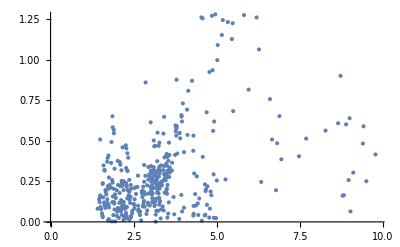

```mathematica
ListPlot[Transpose[{Map[First[#]&,Values[dataset1]],Map[Abs[First[#]-Last[#]]&,Values[dataset1]]}]]
```

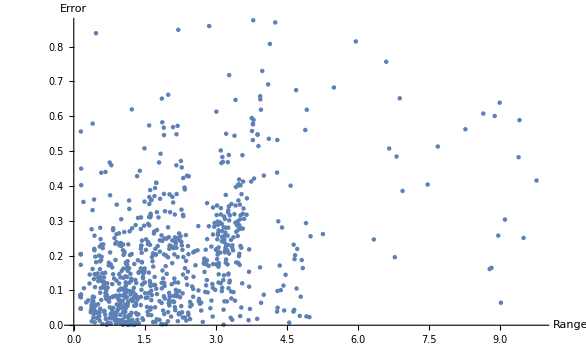

```mathematica
dt = Join[dataset,dataset1];
ListPlot[Transpose[{Map[First[#]&,Values[dt]],Map[Abs[First[#]-Last[#]]&,Values[dt]]}],AxesLabel->{Style["Range",15,Black],Style["Error",15,Black]}]
```

### There should be an issue here....

```mathematica
calculateError[tnet,testing]
```

0.0806686